# λd DCA

## tpd=1.13,tpp=0.49,Udd=8.5,Upp=0

## beta=16, L=4*4

```mathematica
dcan4by4b16Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcalambdad4by4b16Upp0={0.068802793 ,0.103740849 ,0.151425126 ,0.215637531 ,0.329753062 ,0.481274795 ,0.665127312 ,0.643191096 ,0.477346313 ,0.323446879 ,0.19367345 ,0.107570814 ,0.051533715};
```

```mathematica
dcalambdadvsn4by4b16Upp0=Table[{dcan4by4b16Upp0[[i]],dcalambdad4by4b16Upp0[[i]]},{i,1,13}];
```

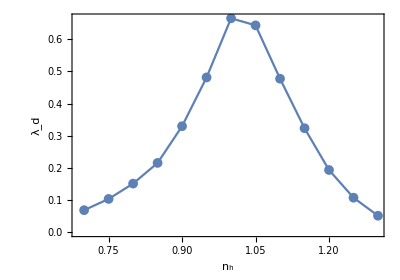

```mathematica
dcalambdadvsn4by4varybeta0=ListPlot[{dcalambdadvsn4by4b16Upp0(*,dcalambdadvsn4by4b24Upp0*)},PlotMarkers->{Automatic,10},(*PlotLegends->Placed[LineLegend[{"β=8","β=16","β=24"},LabelStyle->{14},LegendLayout->{"Row",4}],{0.15,0.7}],*)Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","λ_d","L=4*4"},Joined->True]
```